# State Space Representation (version 05 - 10 - 2022)

## Basins of Attraction and their Fields (in cyclic and acyclic CAs)

### ECA 110 with cyclic configurations of sizes 5 and 7

```mathematica
BAField[110,2,1,5]
```

-Graphics-

```mathematica
BAField[110,2,1,7]
```

-Graphics-

```mathematica
BasinsOfAttraction[110,2,1,7]
```

{-Graphics-,-Graphics-}

```mathematica
BasinsOfAttraction[110,2,1,5]
```

{-Graphics-}

```mathematica
GoEs[-Graphics-]//Length
```

42

### Analysis of the basins of attraction

#### Fixed points

```mathematica
FixedPoints[BAField[110,2,1,5]]
Print@Graph[#,PlotTheme->"Classic"]&/@%;
```

{{0,0,0,0,0}->{0,0,0,0,0}}

-Graphics-

```mathematica
FixedPoints[BAField[110,2,1,7]]
Print@Graph[#,PlotTheme->"Classic"]&/@%;
```

{{0,0,0,0,0,0,0}->{0,0,0,0,0,0,0}}

-Graphics-

#### Limit cycles

```mathematica
LimitCycles[BAField[110,2,1,5]]
Print@Graph[#,PlotTheme->"Classic"]&/@%;
```

{}

```mathematica
LimitCycles[BAField[110,2,1,7]]
Print@Graph[#,PlotTheme->"Classic"]&/@%;
First@%%//Length
```

{{{0,0,0,1,0,1,1}->{0,0,1,1,1,1,1},{0,0,1,1,1,1,1}->{0,1,1,0,0,0,1},{0,1,1,0,0,0,1}->{1,1,1,0,0,1,1},{1,1,1,0,0,1,1}->{0,0,1,0,1,1,0},{0,0,1,0,1,1,0}->{0,1,1,1,1,1,0},{0,1,1,1,1,1,0}->{1,1,0,0,0,1,0},{1,1,0,0,0,1,0}->{1,1,0,0,1,1,1},{1,1,0,0,1,1,1}->{0,1,0,1,1,0,0},{0,1,0,1,1,0,0}->{1,1,1,1,1,0,0},{1,1,1,1,1,0,0}->{1,0,0,0,1,0,1},{1,0,0,0,1,0,1}->{1,0,0,1,1,1,1},{1,0,0,1,1,1,1}->{1,0,1,1,0,0,0},{1,0,1,1,0,0,0}->{1,1,1,1,0,0,1},{1,1,1,1,0,0,1}->{0,0,0,1,0,1,1}}}

-Graphics-

14

#### Garden-of-Eden (GoE) configurations

```mathematica
GoEs[BAField[110,2,1,5]]
%//Length
```

{{0,0,0,0,1},{0,0,0,1,0},{0,0,1,0,0},{0,0,1,0,1},{0,1,0,0,0},{0,1,0,0,1},{0,1,0,1,0},{1,0,0,0,0},{1,0,0,1,0},{1,0,1,0,0}}

10

```mathematica
GoEs2FixedPoint[BAField[110,2,1,5],{0,0,0,0,0}]
%//Length
```

{{0,0,0,0,1},{0,0,0,1,0},{0,0,1,0,0},{0,0,1,0,1},{0,1,0,0,0},{0,1,0,0,1},{0,1,0,1,0},{1,0,0,0,0},{1,0,0,1,0},{1,0,1,0,0}}

10

```mathematica
GoEs2FixedPoint[BAField[110,2,1,7],{0,0,0,0,0,0,0}]
%//Length
```

{{0,1,0,1,0,1,1},{0,1,0,1,1,0,1},{0,1,1,0,1,0,1},{1,0,1,0,1,0,1},{1,0,1,0,1,1,0},{1,0,1,1,0,1,0},{1,1,0,1,0,1,0}}

7

```mathematica
GoEs[BAField[110,2,1,7]]
%//Length
```

{{0,0,0,0,0,0,1},{0,0,0,0,0,1,0},{0,0,0,0,1,0,0},{0,0,0,0,1,0,1},{0,0,0,1,0,0,0},{0,0,0,1,0,0,1},{0,0,0,1,0,1,0},{0,0,1,0,0,0,0},{0,0,1,0,0,0,1},{0,0,1,0,0,1,0},{0,0,1,0,1,0,0},{0,0,1,0,1,0,1},{0,0,1,0,1,1,1},{0,0,1,1,1,0,1},{0,1,0,0,0,0,0},{0,1,0,0,0,0,1},{0,1,0,0,0,1,0},{0,1,0,0,1,0,0},{0,1,0,0,1,0,1},{0,1,0,0,1,1,1},{0,1,0,1,0,0,0},{0,1,0,1,0,0,1},{0,1,0,1,0,1,0},{0,1,0,1,0,1,1},{0,1,0,1,1,0,1},{0,1,0,1,1,1,0},{0,1,1,0,1,0,1},{0,1,1,1,0,0,1},{0,1,1,1,0,1,0},{1,0,0,0,0,0,0},{1,0,0,0,0,1,0},{1,0,0,0,1,0,0},{1,0,0,1,0,0,0},{1,0,0,1,0,1,0},{1,0,0,1,0,1,1},{1,0,0,1,1,1,0},{1,0,1,0,0,0,0},{1,0,1,0,0,1,0},{1,0,1,0,0,1,1},{1,0,1,0,1,0,0},{1,0,1,0,1,0,1},{1,0,1,0,1,1,0},{1,0,1,1,0,1,0},{1,0,1,1,1,0,0},{1,1,0,0,1,0,1},{1,1,0,1,0,0,1},{1,1,0,1,0,1,0},{1,1,1,0,0,1,0},{1,1,1,0,1,0,0}}

49

```mathematica
GoEs2LimitCycle[BAField[110,2,1,7],{1,1,0,0,1,1,1}]
%//Length
```

{{0,0,0,0,0,0,1},{0,0,0,0,0,1,0},{0,0,0,0,1,0,0},{0,0,0,0,1,0,1},{0,0,0,1,0,0,0},{0,0,0,1,0,0,1},{0,0,0,1,0,1,0},{0,0,1,0,0,0,0},{0,0,1,0,0,0,1},{0,0,1,0,0,1,0},{0,0,1,0,1,0,0},{0,0,1,0,1,0,1},{0,0,1,0,1,1,1},{0,0,1,1,1,0,1},{0,1,0,0,0,0,0},{0,1,0,0,0,0,1},{0,1,0,0,0,1,0},{0,1,0,0,1,0,0},{0,1,0,0,1,0,1},{0,1,0,0,1,1,1},{0,1,0,1,0,0,0},{0,1,0,1,0,0,1},{0,1,0,1,0,1,0},{0,1,0,1,1,1,0},{0,1,1,1,0,0,1},{0,1,1,1,0,1,0},{1,0,0,0,0,0,0},{1,0,0,0,0,1,0},{1,0,0,0,1,0,0},{1,0,0,1,0,0,0},{1,0,0,1,0,1,0},{1,0,0,1,0,1,1},{1,0,0,1,1,1,0},{1,0,1,0,0,0,0},{1,0,1,0,0,1,0},{1,0,1,0,0,1,1},{1,0,1,0,1,0,0},{1,0,1,1,1,0,0},{1,1,0,0,1,0,1},{1,1,0,1,0,0,1},{1,1,1,0,0,1,0},{1,1,1,0,1,0,0}}

42

#### Non-GoE configurations leading to fixed points or cycle limits

```mathematica
Configs2FixedPoint[BAField[110,2,1,5],{0,0,0,0,0}]
%//Length
```

{{0,0,0,1,1},{0,0,1,1,0},{0,0,1,1,1},{0,1,0,1,1},{0,1,1,0,0},{0,1,1,0,1},{0,1,1,1,0},{0,1,1,1,1},{1,0,0,0,1},{1,0,0,1,1},{1,0,1,0,1},{1,0,1,1,0},{1,0,1,1,1},{1,1,0,0,0},{1,1,0,0,1},{1,1,0,1,0},{1,1,0,1,1},{1,1,1,0,0},{1,1,1,0,1},{1,1,1,1,0},{1,1,1,1,1}}

21

```mathematica
Configs2FixedPoint[BAField[110,2,1,7],{0,0,0,0,0,0,0}]
%//Length
```

{{1,1,1,1,1,1,1}}

1

```mathematica
Configs2LimitCycle[BAField[110,2,1,7],{0,1,0,1,1,0,0}]
%//Length
```

{{0,0,0,0,0,1,1},{0,0,0,0,1,1,0},{0,0,0,0,1,1,1},{0,0,0,1,1,0,0},{0,0,0,1,1,0,1},{0,0,0,1,1,1,0},{0,0,0,1,1,1,1},{0,0,1,0,0,1,1},{0,0,1,1,0,0,0},{0,0,1,1,0,0,1},{0,0,1,1,0,1,0},{0,0,1,1,0,1,1},{0,0,1,1,1,0,0},{0,0,1,1,1,1,0},{0,1,0,0,0,1,1},{0,1,0,0,1,1,0},{0,1,0,1,1,1,1},{0,1,1,0,0,0,0},{0,1,1,0,0,1,0},{0,1,1,0,0,1,1},{0,1,1,0,1,0,0},{0,1,1,0,1,1,0},{0,1,1,0,1,1,1},{0,1,1,1,0,0,0},{0,1,1,1,0,1,1},{0,1,1,1,1,0,0},{0,1,1,1,1,0,1},{0,1,1,1,1,1,1},{1,0,0,0,0,0,1},{1,0,0,0,0,1,1},{1,0,0,0,1,1,0},{1,0,0,0,1,1,1},{1,0,0,1,0,0,1},{1,0,0,1,1,0,0},{1,0,0,1,1,0,1},{1,0,1,0,0,0,1},{1,0,1,0,1,1,1},{1,0,1,1,0,0,1},{1,0,1,1,0,1,1},{1,0,1,1,1,0,1},{1,0,1,1,1,1,0},{1,0,1,1,1,1,1},{1,1,0,0,0,0,0},{1,1,0,0,0,0,1},{1,1,0,0,0,1,1},{1,1,0,0,1,0,0},{1,1,0,0,1,1,0},{1,1,0,1,0,0,0},{1,1,0,1,0,1,1},{1,1,0,1,1,0,0},{1,1,0,1,1,0,1},{1,1,0,1,1,1,0},{1,1,0,1,1,1,1},{1,1,1,0,0,0,0},{1,1,1,0,0,0,1},{1,1,1,0,1,0,1},{1,1,1,0,1,1,0},{1,1,1,0,1,1,1},{1,1,1,1,0,0,0},{1,1,1,1,0,1,0},{1,1,1,1,0,1,1},{1,1,1,1,1,0,1},{1,1,1,1,1,1,0}}

63

```mathematica
Configs2LimitCycle[BAField[110,2,1,5],{0,0,0,0,0}]
%//Length
```

{}

0

### Relation with reversibility

```mathematica
AllBAFields[150,2,1,10]
```

{1,-Graphics-}

{2,-Graphics-}

{3,-Graphics-}

{4,-Graphics-}

{5,-Graphics-}

{6,-Graphics-}

{7,-Graphics-}

{8,-Graphics-}

```mathematica
Manipulate[
Labeled[
Framed[
GraphPlot[Flatten@Table[{n->FromDigits[CellularAutomaton[rn,IntegerDigits[n,2,m]],2]},{n,0,2^m-1}],
DirectedEdges->True,GraphLayout-> Embedding, PlotTheme->"Classic"]],
Style[Text[Row[{"rule ",rn,"    size ",m}]],14],Top],
{{rn,240,"Rule number"},0,255,1},{{m,3,"Number of cells"},1,12,1},{Embedding,{"SpiralEmbedding","RadialEmbedding"}}]
```

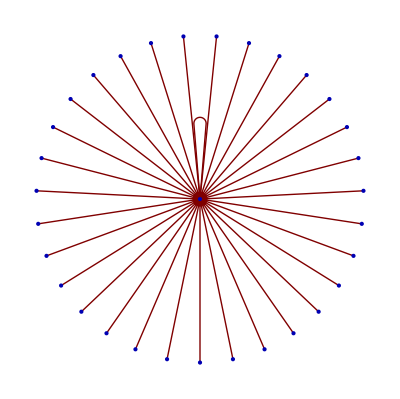
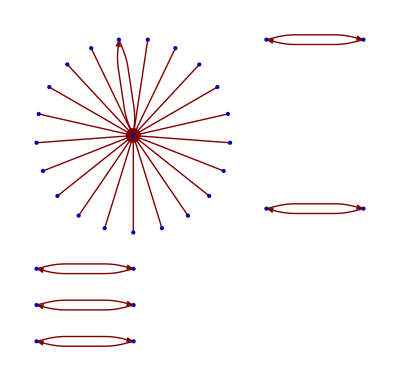
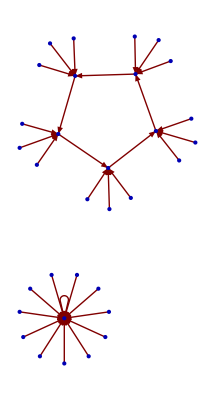
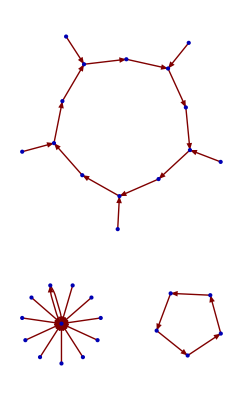
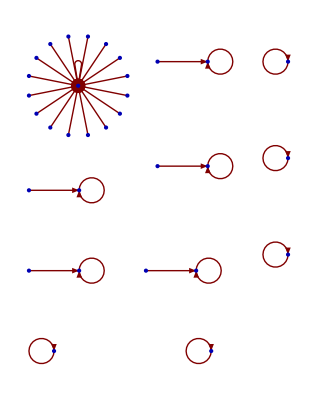
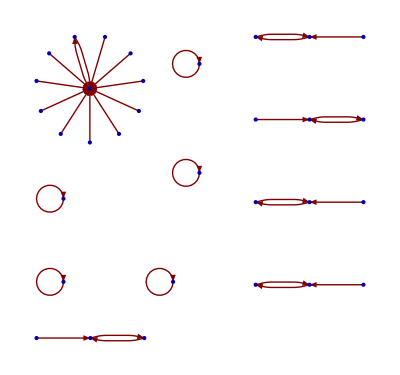
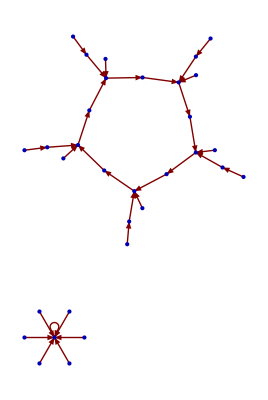
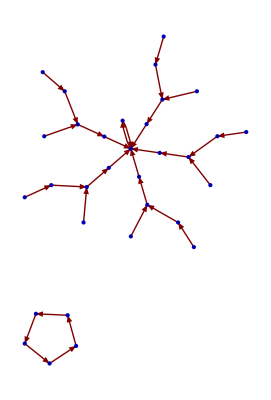

```mathematica
BAField[#,2,1,5,cyclic]&/@(First/@AllEquivalenceRuleClasses[2,1])
```

### Acyclic configurations (with low order)

```mathematica
BAField[110,2,1,1,radial,acyclic]
```

-Graphics-

```mathematica
BAField[110,2,1,2,radial,acyclic]
```

-Graphics-

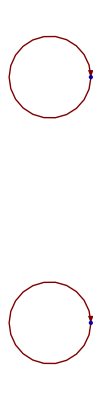

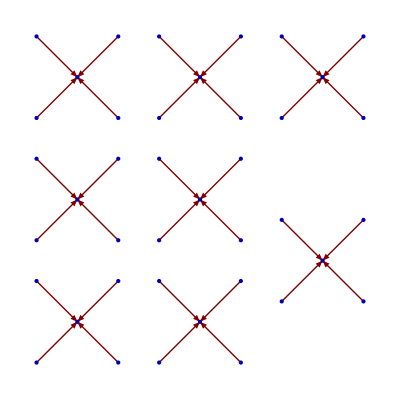

```mathematica
BAField[170,2,1,1,,acyclic]
```

{1,-Graphics-}

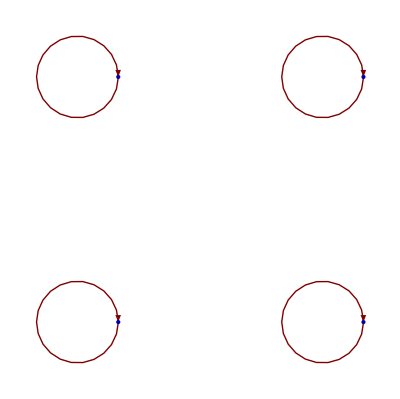
{2,-Graphics-}

{1,-Graphics-}

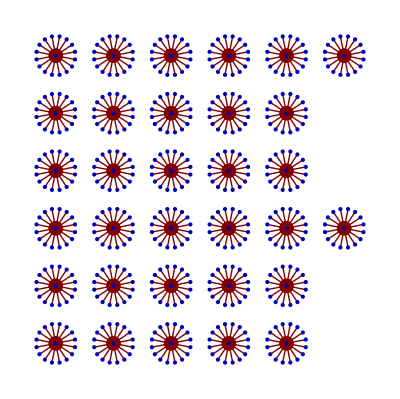
{2,-Graphics-}

```mathematica
AllBAFields[150,2,1,2,,acyclic]
```

```mathematica
AllBAFields[204,2,1,2,,acyclic]
```

{1,-Graphics-}

{2,-Graphics-}

{1,-Graphics-}

{2,-Graphics-}

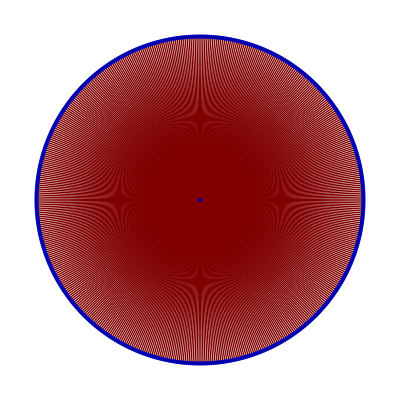
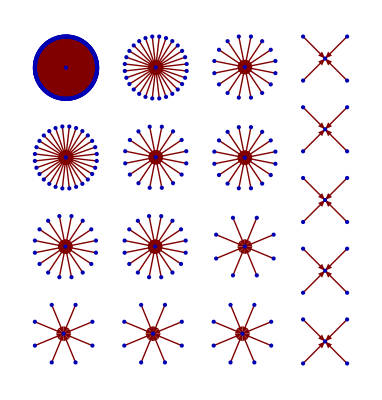
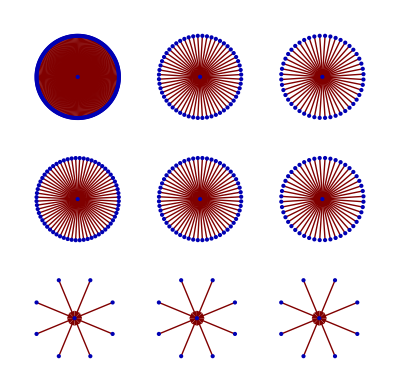
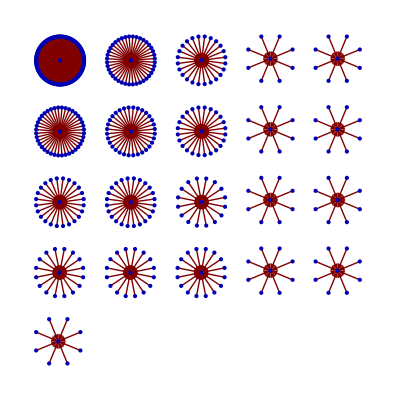
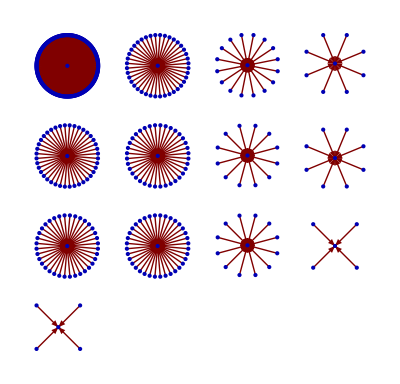
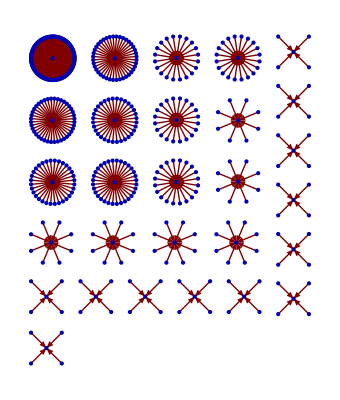
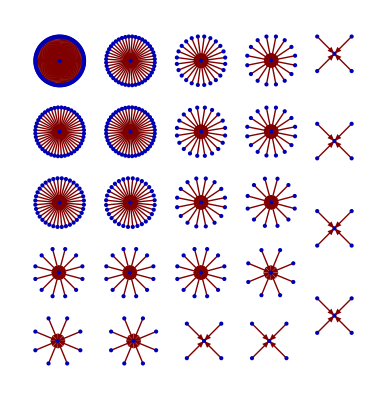
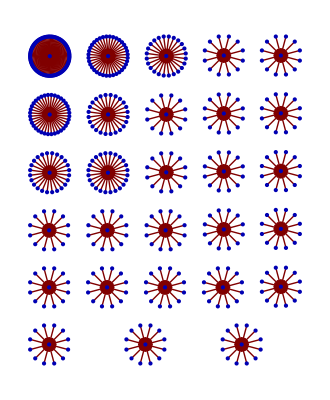
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
BAField[#,2,1,2,,acyclic]&/@(First/@AllEquivalenceRuleClasses[2,1])
```

## Space State as a Cantor Set (cyclic CAs)

```mathematica
(*  Coordinate {x,y}={0,0} is at the bottom, left-most corner.  *)
(*  Each x corresponds to an initial configuration and each y to the corresponding configuration after 1 iteration of the rule *)
With[{rn=170,m=3},Table[{n,FromDigits[CellularAutomaton[rn,IntegerDigits[n,2,m]],2]},{n,0,2^m-1}]]
```

{{0,0},{1,2},{2,4},{3,6},{4,1},{5,3},{6,5},{7,7}}

```mathematica
Manipulate[
Labeled[
Framed[
Graphics[
Point[Table[{n,FromDigits[CellularAutomaton[rn,IntegerDigits[n,2,m]],2]},{n,0,2^m-1}]]]],
Style[Text[Row[{"rule ",rn,"    size ",m}]],14],Top],
{{rn,204,"rule number"},0,255,1},{{m,3,"number of cells"},1,12,1}]
```